/home/zack/cantera/ratematrix

{{6,9,0.0167587,78,6},{9,19,0.0741256,332,9},{12,48,0.312732,1225,12},{15,89,1.25673,3588,15},{18,177,6.19765,9583,18},{21,298,30.5287,22616,21},{24,516,143.265,50049,24},{27,807,649.632,102480,27}}

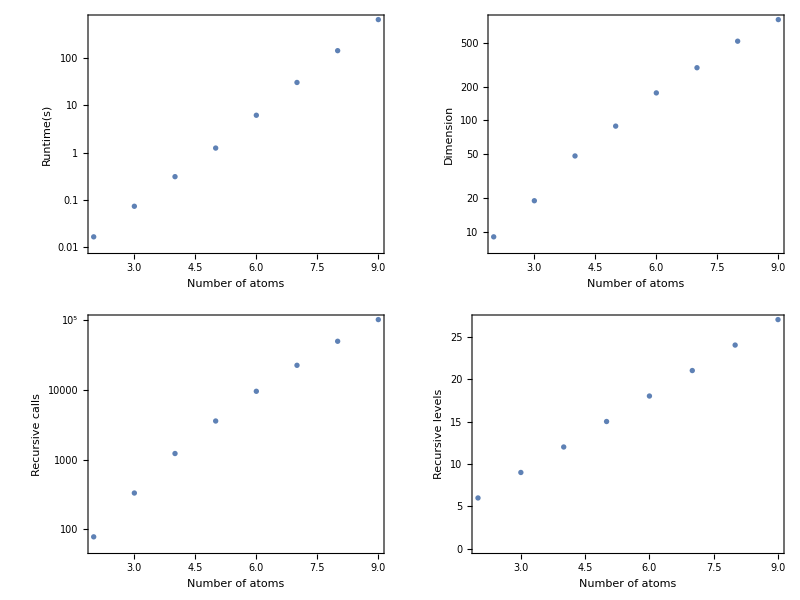

logplot.pdf

```mathematica
SetDirectory[NotebookDirectory[]]
dat=Import["runs.dat"]
p=Grid[{{ListLogPlot[{#[[1]]/3,#[[2]]}&/@dat[[All,{1,3}]],ImageSize->300,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Runtime(s)"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black]],ListLogPlot[{#[[1]]/3,#[[2]]}&/@dat[[All,{1,2}]],ImageSize->300,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Dimension"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black]]},{ListLogPlot[{#[[1]]/3,#[[2]]}&/@dat[[All,{1,4}]],ImageSize->300,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Recursive calls"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black]],ListPlot[{#[[1]]/3,#[[2]]}&/@dat[[All,{1,5}]],ImageSize->300,Frame->True,Axes->False,FrameLabel->{"Number of atoms","Recursive levels"}, FrameStyle->Directive[Black,AbsoluteThickness[2]],LabelStyle->Directive[16,Black]]}}]
Export["logplot.pdf",p]
```